## This program gets the natural response (V_s=0) of a simple parallel RLC circuit with no external source.

```mathematica
Clear["Global`*"]
r =12(*Input["Enter The Value Of Resistance"]*);
capacitor=1*10(*Input["Enter The Value Of Capacitance"]*);
l=0.15(*Input["Enter The Value Of L"]*);
Subscript[ω, 0]=√(1/(l capacitor));
ζ = 1/(2 Subscript[ω, 0] r capacitor);
eqn1=Subscript[V, c]''[t]+2 ζ Subscript[ω, 0] Subscript[V, c]'[t]+Subscript[ω, 0]^2 Subscript[V, c][t]==0;
DSolve[{eqn1, Subscript[V, c]''[0]==1, Subscript[V, c]'[0]==0},Subscript[V, c][t],t][[1]]//N//Simplify
capVoltage=DSolve[{eqn1, Subscript[V, c]''[0]==1, Subscript[V, c]'[0]==0},Subscript[V, c][t],t][[1]]//N//Simplify
(*Print [ζ]
Print[Subscript[V, c]''[0]==1]
Print[Subscript[V, c]'[0]==0]*)
If[ζ<1,Style["ζ<1 → underdamped",Blue,24], If[ζ>1, Style["ζ>1 → overdamped",Blue,24], Style["ζ=1 → critically damped",Blue,24]]]
Style[capVoltage,Blue,24]
```

DSolve::deqn: Equation or list of equations expected instead of False in the first argument {0.+0.666667 capVoltage==0,False,True}.

{capVoltage==0,False,True}

DSolve::deqn: Equation or list of equations expected instead of False in the first argument {0.+0.666667 capVoltage==0,False,True}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of capVoltage==0.

Hold[{capVoltage==0,False,True}]

ζ<1 → underdamped

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of capVoltage==0.

Hold[Style[capVoltage,Blue,24]]

## This program gets the natural response (V_s=0) of a simple series RLC circuit with no external source.

{V1[t]→ⅇ^(-5.55556×10^7 t) (1. Cos[1.24226×10^8 t]+0.447214 Sin[1.24226×10^8 t])}

1/(√6)

ζ<1 → underdamped

{V1[t]→ⅇ^(-5.55556×10^7 t) (1. Cos[1.24226×10^8 t]+0.447214 Sin[1.24226×10^8 t])}

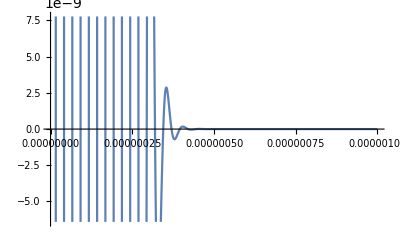

```mathematica
Clear["Global`*"]
R1 =1(*Input["Enter The Value Of Resistance"]*);
Cap1=6*10^-9(*Input["Enter The Value Of Capacitance"]*);
L1=9*10^-9(*Input["Enter The Value Of L"]*);
ω1=1/(√(L1 Cap1));
ζ1 = R1/(2 L1 ω1);
eqn2=V1''[t]+2 ζ1 ω1 V1'[t]+ω1^2 V1[t]==0;
capVoltage2=DSolve[{eqn2, V1'[0]==5, V1[0]==1}, V1[t],t][[1]]//N//Simplify
Style[ζ1,Blue,24]
If[ζ1<1,Style["ζ<1 → underdamped",Blue,24], If[ζ1>1, Style["ζ>1 → overdamped",Blue,24], Style["ζ=1 → critically damped",Blue,24]]]
Style[capVoltage2,Blue,20]
Vsol[t_]:=V1[t] /.capVoltage2
Plot[Vsol[t], {t, 0, 10^-6}, PlotRange-> Automatic]
```

```mathematica
ζa=2
StringForm["a = `",a]
```

2

StringForm::sfq: Unmatched backquote in a = `.

a = `